```mathematica
(*Author: Oleg Kravchenko, 
Date: 11/09/15; 
Upd.01: 23/01/16*)
```

```mathematica
ClearAll["Global`*"]
```

### CIP - BS plots; Ref: NIFS-778, Basis Set Approach in the Constrained Interpolation Profile Method, T. Utsumi, J. Koga, T. Yabe, Y. Ogata, E. Matsunaga, T. Aoki and M. Sekine, July 2003

### Parameters;

```mathematica
ImgSz=250;
```

### Basic Functions;

```mathematica
BasisCIPBS[x_,k_,K_]:=Module[{ϕList,ϕL,ϕR,ϕ},
ϕK[x,K]:=Sum[Subscript[a, i] x^i,{i,0,2K+1,1}];
EqnSysL[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->-h)==0,{l,0,K,1}]
}//Flatten;
EqnSysR[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->h)==0,{l,0,K,1}]
}//Flatten;
ϕList={
ϕL=ϕK[x,K]/.Solve[EqnSysL[k,K],CoefficientList[ϕK[x,K],x]] ,
ϕR=ϕK[x,K]/.Solve[EqnSysR[k,K],CoefficientList[ϕK[x,K],x]],
(*ϕ=ϕL θ[x+1]+ϕR θ[x]*)
ϕ=Piecewise[{
{ϕL[[1]],-h≤x≤0},
{ϕR[[1]],0≤x≤h}
}]
}//Flatten
]
```

#### Manipulation;

```mathematica
Manipulate[BasisCIPBS[x,k,indK][[1;;3]],{{indK,0,"K"},0,5,1},{k,0,indK,1}]
```

```mathematica
Manipulate[
Column[{BasisCIPBS[x,k,indK][[1;;2]]//Column,
Plot[Evaluate[BasisCIPBS[x,k,indK][[3]]/.h->1],{x,-1,1},ImageSize->ImgSz]},Alignment->Center],
{{indK,0,"K"},0,7,1},{k,0,indK,1}]
```

```mathematica
f[x_]:=Sin[π x^5] x^7(1-x)
```

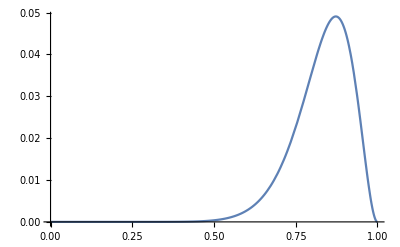

```mathematica
Plot[f[x],{x,0,1}]
```

#### Interpolation;

4

0

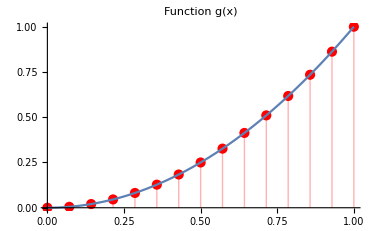
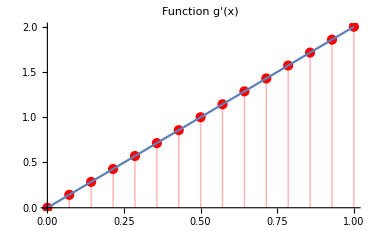
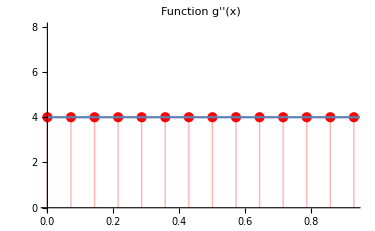

```mathematica
(*Function to be interpolated*)
g0[x_]:=x^2(*Sin[π x^5] x^7(1-x)*)
g1[x_]:=D[g0[x],{x,1}]//Evaluate
g2[x_]:=2+0*x+D[g0[x],{x,2}]//Evaluate
g3[x_]:=0*x+D[g0[x],{x,3}]//Evaluate
(*Parameters*)
a=0;
b=1;
nx=15;
hx=(b-a)/(nx-1);
(*Arrays*)
xTbl=Table[a+k*hx,{k,0,nx-1,1}]//N;
g0Tbl=g0@xTbl;
g1Tbl=g1@xTbl;
g2Tbl=g2@xTbl
g3Tbl=g3@xTbl

Row[{Show[{ListPlot[Partition[Riffle[xTbl,g0Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g(x)",PlotLegends->g0[x]],
Plot[g0[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant",PlotRange->All]}],Show[{ListPlot[Partition[Riffle[xTbl,g1Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g'(x)",PlotLegends->g1[x]],
Plot[g1[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,g2Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g''(x)",PlotLegends->g2[x]],
Plot[g2[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant"]}]
}]
```

#### CIP-BS^0;

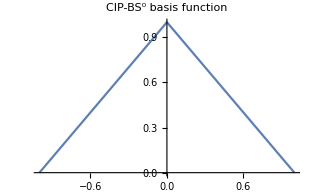
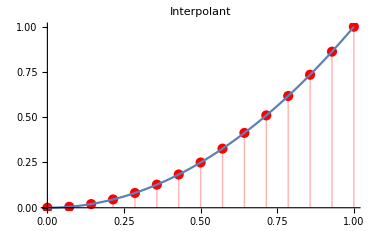
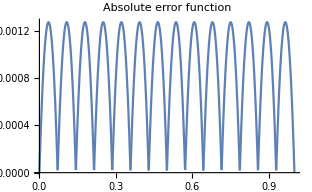

```mathematica
(*Basis Function*)
ϕ00=BasisCIPBS[x,0,0][[3]];
(*Matrix of values*)
ϕ00Matrix=Table[If[i==j,((ϕ00/.h->hx)/.x->x-xTbl[[i]]//Simplify)/.x->xTbl[[i]],0],{i,1,nx},{j,1,nx}];
(*Coefficients*)
coeff=LinearSolve[ϕ00Matrix,g0Tbl];
ϕApprox=Sum[coeff[[k]](ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify,{k,1,nx}];
(*Absolute error function*)
err0[x_]:=Abs[g0[x]-ϕApprox];
(*Plots*)
Row[{Plot[ϕ00/.h->1,{x,-1,1},ImageSize->1.25ImgSz,PlotLabel->"CIP-BS^0 basis function"],
Show[{ListPlot[Partition[Riffle[xTbl,g0Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Interpolant",PlotLegends->g0[x]],
Plot[g0[x],{x,a,b},ImageSize->1.25ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}],
Plot[err0[x],{x,a,b},ImageSize->1.25ImgSz,PlotLabel->"Absolute error function",PlotRange->All]},Spacer[20]]
```

Part::partd: Part specification 4 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 4 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 4 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification 4 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 0 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 4 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification 4. ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 4. ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 4. ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

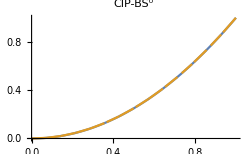
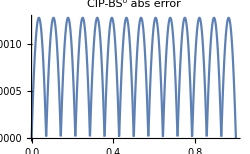
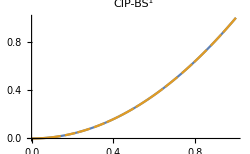
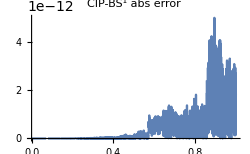
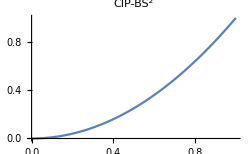
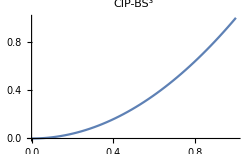
Interpolation of g(x)=TraditionalForm`x^2
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
(*CIP-BS^0*)
Clear[ϕ00,gApprox0]
ϕ00=BasisCIPBS[x,0,0][[3]];
gApprox0=Sum[g0Tbl[[k]](ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify,{k,1,nx}];
(*CIP-BS^1*)
Clear[ϕ00,ϕ01,gApprox1]
ϕ00=BasisCIPBS[x,0,1][[3]];
ϕ01=BasisCIPBS[x,1,1][[3]];
gApprox1=Sum[(g0Tbl[[k]](ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g1Tbl[[k]](ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx}];
(*CIP-BS^2*)
Clear[ϕ00,ϕ01,ϕ02,gApprox2]
ϕ00=BasisCIPBS[x,0,2][[3]];
ϕ01=BasisCIPBS[x,1,2][[3]];
ϕ02=BasisCIPBS[x,2,2][[3]];
gApprox2=Sum[(g0Tbl[[k]](ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g1Tbl[[k]](ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g2Tbl[[k]](ϕ02/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx}];
(*CIP-BS^3*)
Clear[ϕ00,ϕ01,ϕ02,ϕ03,gApprox3]
ϕ00=BasisCIPBS[x,0,3][[3]];
ϕ01=BasisCIPBS[x,1,3][[3]];
ϕ02=BasisCIPBS[x,2,3][[3]];
ϕ03=BasisCIPBS[x,3,3][[3]];
gApprox3=Sum[(g0Tbl[[k]](ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g1Tbl[[k]](ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g2Tbl[[k]](ϕ02/.h->hx)/.x->x-xTbl[[k]]//Simplify)+(g3Tbl[[k]](ϕ03/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx}];

imgTmp=Column[{
"Interpolation of g(x)="<>ToString[g0[x]//TraditionalForm],
Row[{Plot[{g0[x],gApprox0},{x,a,b},ImageSize->ImgSz,PlotLabel->"CIP-BS^0"],Plot[{Abs[g0[x]-gApprox0]},{x,a,b},ImageSize->ImgSz,PlotRange->All,PlotLabel->"CIP-BS^0 abs error"]}],
Row[{Plot[{g0[x],gApprox1},{x,a,b},ImageSize->ImgSz,PlotLabel->"CIP-BS^1"],Plot[{Abs[g0[x]-gApprox1]},{x,a,b},ImageSize->ImgSz,PlotRange->All,PlotLabel->"CIP-BS^1 abs error"]}],
Row[{Plot[{g0[x],gApprox2},{x,a,b},ImageSize->ImgSz,PlotLabel->"CIP-BS^2"],Plot[{Abs[g0[x]-gApprox2]},{x,a,b},ImageSize->ImgSz,PlotRange->All,PlotLabel->"CIP-BS^2 abs error"]}],
Row[{Plot[{g0[x],gApprox3},{x,a,b},ImageSize->ImgSz,PlotLabel->"CIP-BS^3"],Plot[{Abs[g0[x]-gApprox3]},{x,a,b},ImageSize->ImgSz,PlotRange->All,PlotLabel->"CIP-BS^3 abs error"]}]
},Center]
```

```mathematica
Export["C:\\Users\\oleg-2\\Dropbox\\Collaboration\\nb\\img\\png\\interp001_x^2.png",imgTmp]
```

C:\Users\oleg-2\Dropbox\Collaboration\nb\img\png\interp001_x^2.png

```mathematica
D[x^2 Sin[π x],x,x]
```

4 π x Cos[π x]+2 Sin[π x]-π^2 x^2 Sin[π x]

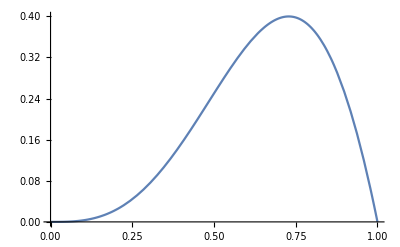

```mathematica
Plot[x^2 Sin[π x],{x,0,1}]
```

```mathematica
Integrate[x+1,x]
Integrate[%,x]
```

x+x^2/2

1/2 (x^2+x^3/3)

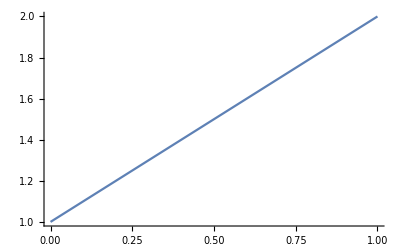

```mathematica
Plot[x+1,{x,0,1}]
```